```mathematica
vmax=5;
p=0.98;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho*0.1,0.001];
dmax=Round[rho*1.2,0.001];
dd=Round[(dmax-dmin)/22,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<21,i++;
Print[dmin+i*dd]
]
For[i=1,i<4,i++;
Print[i*rho]
]
```

0.005  :Transition density!!!

0.

0.006 : Max density

0.

List of simulated values:

0.

0.

0.

«19 more identical outputs»

0.01

0.015

0.02

0.02

16384. = L

786 = N

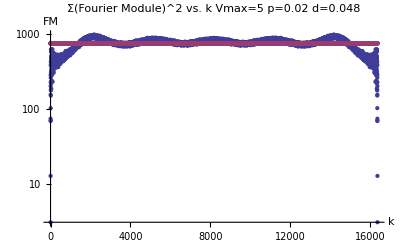

748.338 = N*(L-N)/(L-1)

809.116 = Mean of o.7 largest values

1.226×10^7 = Sum of All L-1 Valus

1.226×10^7 = N*(L-N)

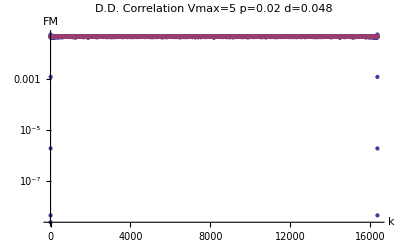

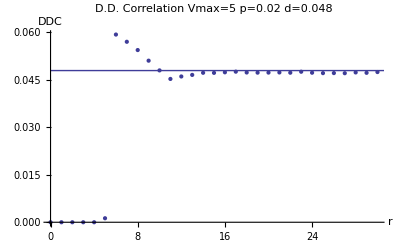

0.0479155 = (N-1)/(L-1)

0.0480014 = Mean of o.9 largest values

0.0479155 = Mean of all L-1 values

0.001222 = STDV of all L-1 values

0.0255032 = STDV/Mean

785. = Sum of All L Valus

785 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,2.33735×10^-9}

{1,-1.01638×10^-10}

{2,4.36554×10^-9}

{3,-4.17702×10^-9}

{4,1.91002×10^-6}

{5,0.00126463}

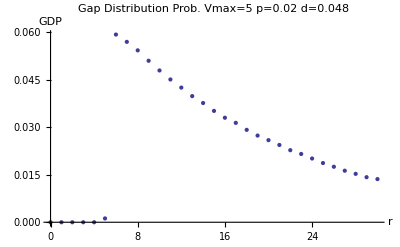

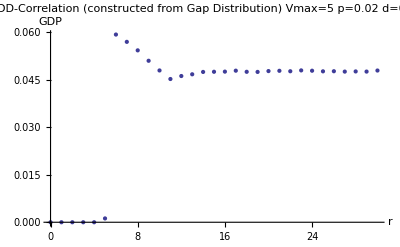

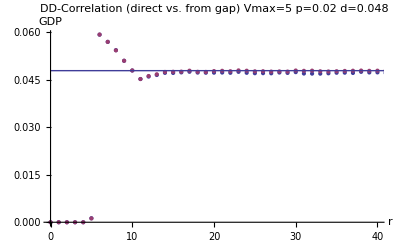

```mathematica
d="0.048";
p="0.02"
vmax="5";
n=16384.000;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/fourier.1d.averaged.d";

b=".p"<>p<>".v5.txt";
g=".p"<>p<>".v5.txt";
c=a<>d<>b;
gap="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/GapD.d.";
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/ddensitycorrelation.d";
h="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/DDCCheck.d";
l=h<>d<>g;
f=e<>d<>g;
gapadd=gap<>d<>g;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
DDCCheck=ReadList[l,{Number,Number}];
gapd=ReadList[gapadd,{Number,Number}];
bitf2=bitF[[All,2]];
randomf=Table[{i,(n-m)*m/(n-1)},{i,0,16383}];
ListLogPlot[{bitF,randomf},PlotLabel->"Σ(Fourier Module)^2 vs. k  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
prand=(m-1)/(n-1);
random=Table[{i,prand},{i,0,16383}];
pic6=ListLogPlot[{density,random},PlotLabel->"D.D. Correlation Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
pic1=ListPlot[density,PlotLabel->"D.D. Correlation Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,DDC},PlotRange->{{0,30},Full}];
pic2=ListLinePlot[random];
Show[pic1,pic2]
prand  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
mean=Mean[Delete[density2,1]] "= Mean of all L-1 values"
stdv=StandardDeviation[Delete[density2,1]]  "= STDV of all L-1 values"
StandardDeviation[Delete[density2,1]]/Mean[Delete[density2,1]] "= STDV/Mean"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
For[i=0,i<50,i++,
If[density2[[i]]<2*prand/3,
Print[{i-1,density2[[i]]}]
]
]
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,30},Full}]
pic7=ListPlot[DDCCheck,PlotLabel->"DD-Correlation (constructed from Gap Distribution) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,30},Full}]
pic3=ListPlot[density,PlotLabel->"GDP against DDC  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP/DDC"},PlotRange->{{0,30},Full}];
pic4=ListLinePlot[gapd];
pic5=ListPlot[gapd];
pic8=ListPlot[{density,DDCCheck},PlotLabel->"DD-Correlation (direct vs. from gap) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,40},Full}];
Show[pic8,pic2]
```